```mathematica
Map[SetOptions[#,
BaseStyle->Directive@@{FontColor->Black},TicksStyle->Directive@@{FontColor->Black},
LabelStyle->Directive@@{FontColor->Black}]&,
{LogPlot,Plot}];
```

```mathematica
cp2radsec[cp_]:=π/(3cp);
radsec2rpm[rs_]:=(30rs)/π;
(* This function reproduces the speed limiting controller in the firmware.
Refer to the original source code for details. *)
cplimits[freq_]:=Module[{
pwmper=1/freq,
cplimit,
limitingBeginsAt,
limitingFullAt
},
cplimit=Max[8pwmper,109 10^-6];
limitingBeginsAt=cplimit 5/4;
limitingFullAt=cplimit/4;
cp2radsec[{limitingFullAt,cplimit,limitingBeginsAt}]
]
```

```mathematica
pwmFrequencyTicks=Table[i,{i,5000,100000,5000}];

radianSecondTicks=1000{2,3,4,5,6,7,8,9,10,12,15,20,25,30,40,50};

LogPlot[{
cplimits[f][[3]],
cplimits[f][[1]],
cplimits[f][[2]]
},{f,20000,75000},
PlotTheme->"Detailed",
FrameLabel->{
"PWM frequency, Hz",
"Angular speed, electrical radian/second",
None,
"Angular speed, electrical RPM"},
PlotLegends->Placed[LineLegend[{
"[Open loop mode] Duty cycle setpoint limiting begins",
"[Open loop mode] Maximum limiting, zero duty cycle",
"[RPM loop mode] Maximum RPM setpoint"
},LegendLayout->"Row"],{Center,0}],
ImageSize->690,
GridLines->{pwmFrequencyTicks,Table[1000i,{i,1,20}]},
FrameTicks->{
{radianSecondTicks,
Map[{#,radsec2rpm[#]//Round}&,radianSecondTicks]},
{pwmFrequencyTicks,pwmFrequencyTicks}
},
Filling->{1->{2}},
FillingStyle->GrayLevel[0.5,0.22]]
```

-Graphics-

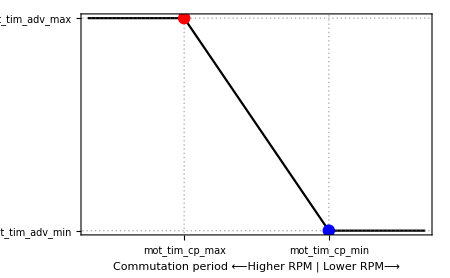

```mathematica
advmin=5;
advmax=15;
cpmax=300;
cpmin=600;
fn[cp_]:=advmin/;cp≥cpmin
fn[cp_]:=advmax/;cp≤cpmax
fn[cp_]:=advmax-(advmax-advmin)*(cp-cpmax)/(cpmin-cpmax);
Margin=200;
plot=Plot[fn[cp],{cp,cpmax-Margin,cpmin+Margin},FrameLabel->{"Commutation period\n⟵Higher RPM  |  Lower RPM⟶","Advance angle"},Frame->{True,True,False,False},PlotTheme->"Detailed",PlotLegends->None,PlotStyle->{Black},
FrameTicks->{
{{{advmin,Style["mot_tim_adv_min",FontColor->Blue]},
{advmax,Style["mot_tim_adv_max",FontColor->Red]}},
{}},
{{{cpmin,Style["mot_tim_cp_min",FontColor->Blue]},
{cpmax,Style["mot_tim_cp_max",FontColor->Red]}},
{}}
},
GridLines->{{cpmin,cpmax},{advmin,advmax}},
ImageSize->450];
Show[{plot,
Graphics[{PointSize[.02],Blue,Point[{cpmin,advmin}]}],
Graphics[{PointSize[.02],Red,Point[{cpmax,advmax}]}]},ImageMargins->5]
```

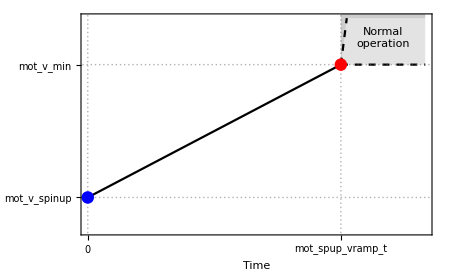

```mathematica
Vspinup=0.5;
Vmin=2.5;
Tspinup=3.0;
Margin=1;
spinupVoltageRamp[t_]:=If[t<Tspinup,Vspinup+(Vmin-Vspinup)t/Tspinup,None];
postSpinupVoltage[t_]:=If[t<Tspinup,None,{Vmin+(t-Tspinup)10,Vmin}];

plot=Plot[{spinupVoltageRamp[t],postSpinupVoltage[t]},{t,0,Tspinup+Margin},FrameLabel->{"Time","Source voltage E_s"},
Frame->{True,True,False,False},
PlotTheme->"Detailed",
PlotLegends->None,
PlotStyle->{Black,{Black,Dashed}},
FrameTicks->{
{{{Vspinup,Style["mot_v_spinup",FontColor->Blue]},
{Vmin,Style["mot_v_min",FontColor->Red]}},{}},
{{{0,Style[0,FontColor->Blue]},
{Tspinup,Style["mot_spup_vramp_t",FontColor->Red]}},{}}
},
PlotRange->{Full,{0,Vmin+0.7}},
GridLines->{{0,Tspinup},{Vspinup,Vmin}},
ImageSize->450,
Filling->{2->4},
FillingStyle->GrayLevel[0.5,0.22]];

Show[{plot,
Graphics[{PointSize[.02],Blue,Point[{0,Vspinup}]}],
Graphics[{PointSize[.02],Red,Point[{Tspinup,Vmin}]}],
Graphics[{Black,Text["Normal\noperation",{Tspinup+0.5,Vmin+0.4}]}]
},
ImageMargins->5]
```